```mathematica
(* TB Incidence for each year *)
```

```mathematica
s4={{27,10},{42,16},{57,35},{72,108},{89,174}}
```

{{27,10},{42,16},{57,35},{72,108},{89,174}}

```mathematica
s5={{27,10},{42,15},{57,31},{72,95},{89,176}}
```

{{27,10},{42,15},{57,31},{72,95},{89,176}}

```mathematica
s6={{27,10},{42,15},{57,30},{72,92},{89,175}}
```

{{27,10},{42,15},{57,30},{72,92},{89,175}}

```mathematica
s7={{27,9},{42,14},{57,26},{72,86},{89,178}}
```

{{27,9},{42,14},{57,26},{72,86},{89,178}}

```mathematica
s8={{27,9},{42,12},{57,23},{72,74},{89,148}}
```

{{27,9},{42,12},{57,23},{72,74},{89,148}}

```mathematica
s9={{27,7},{42,11},{57,20},{72,65},{89,142}}
```

{{27,7},{42,11},{57,20},{72,65},{89,142}}

```mathematica
inc4=Table[{s4[[i,1]],300/96 s4[[i,2]]},{i,Length[s4]}]
inc5=Table[{s4[[i,1]],300/96 s5[[i,2]]},{i,Length[s4]}]
inc6=Table[{s4[[i,1]],300/96 s6[[i,2]]},{i,Length[s4]}]
inc7=Table[{s4[[i,1]],300/96 s7[[i,2]]},{i,Length[s4]}]
inc8=Table[{s4[[i,1]],300/96 s8[[i,2]]},{i,Length[s4]}]
inc9=Table[{s4[[i,1]],300/96 s9[[i,2]]},{i,Length[s4]}]
```

{{27,125/4},{42,50},{57,875/8},{72,675/2},{89,2175/4}}

{{27,125/4},{42,375/8},{57,775/8},{72,2375/8},{89,550}}

{{27,125/4},{42,375/8},{57,375/4},{72,575/2},{89,4375/8}}

{{27,225/8},{42,175/4},{57,325/4},{72,1075/4},{89,2225/4}}

{{27,225/8},{42,75/2},{57,575/8},{72,925/4},{89,925/2}}

{{27,175/8},{42,275/8},{57,125/2},{72,1625/8},{89,1775/4}}

```mathematica
inclog4=Table[{s4[[i,1]],Log[300/96 s4[[i,2]]]},{i,Length[s4]}]
inclog5=Table[{s4[[i,1]],Log[300/96 s5[[i,2]]]},{i,Length[s4]}]
inclog6=Table[{s4[[i,1]],Log[300/96 s6[[i,2]]]},{i,Length[s4]}]
inclog7=Table[{s4[[i,1]],Log[300/96 s7[[i,2]]]},{i,Length[s4]}]
inclog8=Table[{s4[[i,1]],Log[300/96 s8[[i,2]]]},{i,Length[s4]}]
inclog9=Table[{s4[[i,1]],Log[300/96 s9[[i,2]]]},{i,Length[s4]}]
```

{{27,Log[125/4]},{42,Log[50]},{57,Log[875/8]},{72,Log[675/2]},{89,Log[2175/4]}}

{{27,Log[125/4]},{42,Log[375/8]},{57,Log[775/8]},{72,Log[2375/8]},{89,Log[550]}}

{{27,Log[125/4]},{42,Log[375/8]},{57,Log[375/4]},{72,Log[575/2]},{89,Log[4375/8]}}

{{27,Log[225/8]},{42,Log[175/4]},{57,Log[325/4]},{72,Log[1075/4]},{89,Log[2225/4]}}

{{27,Log[225/8]},{42,Log[75/2]},{57,Log[575/8]},{72,Log[925/4]},{89,Log[925/2]}}

{{27,Log[175/8]},{42,Log[275/8]},{57,Log[125/2]},{72,Log[1625/8]},{89,Log[1775/4]}}

```mathematica
lm=NonlinearModelFit[(inclog4+inclog5+inclog6+inclog7+inclog8+inclog9)/6,0.044 x+b,{b},x]
```

FittedModel[2.14911+0.044 x]

```mathematica
lm2=NonlinearModelFit[(inclog4+inclog5+inclog6+inclog7+inclog8+inclog9)/6,a x+b,{b,a},x]
```

FittedModel[1.8329+0.0495089 x]

```mathematica
lm3=LinearModelFit[(inclog4),x,x]
```

FittedModel[1.99748+0.0494129 x]

```mathematica
lm2
```

FittedModel[1.8329+0.0495089 x]

```mathematica
lm2["ParameterConfidenceIntervals"]
```

{{0.967715,2.69809},{0.0354169,0.0636009}}

```mathematica
Log[2]/0.049412890189232034
```

14.0277

```mathematica
Log[2]/0.06314523628543317
```

10.977

```mathematica
Log[2]/0.03568054409303089
```

19.4265

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS
Model | 1 | 115.01 | 115.01
Error | 4 | 0.211619 | 0.0529048
Uncorrected Total | 5 | 115.221 | 
Corrected Total | 4 | 5.95662 |

```mathematica
1-0.21161931116846466/5.956615971279103
```

0.964473

```mathematica
lm3["AdjustedRSquared"]
```

0.970179

```mathematica
Log[2]/15.7
```

0.0441495

```mathematica
N[Log[2]/16]
```

0.0433217

```mathematica
lm2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
b | 1.8329 | 0.271862 | 6.74203 | 0.00666392
a | 0.0495089 | 0.00442805 | 11.1807 | 0.00153352

```mathematica
Log[2]/(0.044)
```

15.7533

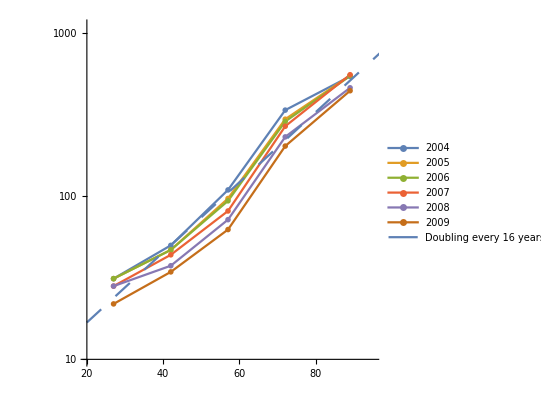

```mathematica
Show[ListLogPlot[{inc4,inc5,inc6,inc7,inc8,inc9},Joined->True,PlotRange->{{20,95},{10,Exp[7]}},PlotLegends->{2004,2005,2006,2007,2008,2009},PlotMarkers->"OpenMarkers",AspectRatio->1,AxesStyle->Thick],Plot[lm2[x],{x,20,100},PlotStyle->Dashing[Large],PlotLegends->{"Doubling every 16 years"}]]
```

```mathematica
s=Import["~/Projects/Minireview/Diseases2.xlsx"][[1]];
```

```mathematica
mrsa=s[[Range[67,73],{1,2}]]
```

{{1.,6.37375},{3.,2.65},{11.,1.7675},{26.,9.90375},{42.,24.355},{57.,46.2937},{80.,111.121}}

```mathematica
wnv=s[[Range[94,101],{1,2}]]
```

{{5.,0.0576923},{15.,0.102564},{25.,0.173077},{35.,0.269231},{45.,0.416667},{55.,0.557692},{65.,0.852564},{75.,1.35256}}

```mathematica
grpBstrep=s[[Range[13,22],{1,2}]]
```

{{0.5,57.65},{1.,0.365},{3.,0.12},{11.,0.18},{26.,2.105},{42.,6.02},{57.,13.55},{70.,20.6},{80.,32.15},{92.,41.85}}

```mathematica
strepn=s[[Range[24,33],{1,2}]]
```

{{0.5,15.05},{1.,12.6},{3.,6.5},{11.,1.45},{26.,2.75},{42.,7.15},{57.,15.9},{70.,19.95},{80.,31.1},{92.,50.05}}

```mathematica
haem=s[[Range[56,65],{1,2}]]
```

{{0.5,9.91},{1.,2.44},{3.,1.23},{11.,0.36},{26.,0.44},{42.,0.67},{57.,1.685},{70.,4.04},{80.,7.475},{92.,12.845}}

```mathematica
s=Import["~/Projects/Minireview/Saudi Arabia-2012-MERS.csv"];
```

```mathematica
mers=s[[Range[2,18,2],{11,10}]]
```

{{5,0.177247},{15,0.639034},{25,3.50355},{35,4.5666},{45,7.0852},{55,17.0427},{65,32.2207},{75,59.1354},{85,74.2385}}

```mathematica
mers[[9,1]]=88
```

88

```mathematica
mrsalm=NonlinearModelFit[mrsa,Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(1.21056+0.044 x)]

```mathematica
merslm=NonlinearModelFit[Drop[mers,-2],Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(0.478414+0.044 x)]

```mathematica
strepnlm=NonlinearModelFit[strepn,Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(-0.0952792+0.044 x)]

```mathematica
grpBstreplm=NonlinearModelFit[grpBstrep,Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(-0.194146+0.044 x)]

```mathematica
haemlm=NonlinearModelFit[Drop[Drop[haem,-2],2],Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(-1.76414+0.044 x)]

```mathematica
wnvlm=NonlinearModelFit[wnv,Exp[0.044x+b],{b},x]
```

FittedModel[ⅇ^(-2.99344+0.044 x)]

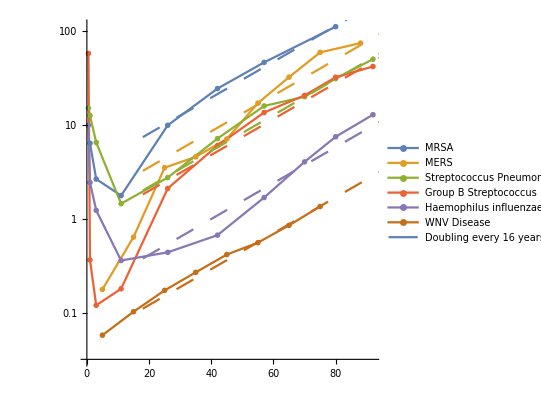

```mathematica
Show[ListLogPlot[{mrsa,mers,strepn,grpBstrep,haem,wnv},Joined->True,PlotLegends->{"MRSA","MERS","Streptococcus Pneumonia","Group B Streptococcus","Haemophilus influenzae","WNV Disease"},PlotMarkers->"OpenMarkers",AspectRatio->1],LogPlot[{mrsalm[x],0.91merslm[x],strepnlm[x],grpBstreplm[x],haemlm[x],wnvlm[x]},{x,18,100},PlotStyle->Dashing[Large],PlotLegends->{"Doubling every 16 years"}]]
```